```mathematica
SetDirectory["g:/git/ProjectionMethodTools/ProjectionMethodToolsJava/code"];
Get["prepPackages.mth"]
```

temp export of kronProd

xx::shdw: Symbol "xx" appears in multiple contexts {"ProjectionInterface`", "Global`"}; definitions in context "ProjectionInterface`" may shadow or be shadowed by other definitions.

why not numbers?

why eval of shock t+1?

done reading ProjectionInterface

## Judd JET Example

### Deterministic Model

#### Model Equations

```mathematica
uFunc[cc_]:=(1/(1+gamma))*cc^(1+gamma)
uPrimeFunc[cc_]:=(D[uFunc[xx],xx]/.xx->cc)

fFunc[kk_]:=AA*kk^alpha;
fPrimeFunc[kk_]:=(D[fFunc[xx],xx]/.xx->kk)

juddDetEqn={kk[t]-(fFunc[kk[t-1]]-cc[t]),uPrimeFunc[cc[t]]-beta*uPrimeFunc[cc[t+1]]*fPrimeFunc[kk[t]]};
newWeightedStochasticBasis[juddDetMod,juddDetEqn]
```

#### Projection Method Specification

```mathematica
{{stateVar,nonStateVar,theShock},modEqns}=GenerateModelCode[juddDetMod];
```

"c:\Program Files\Java\jdk1.7.0_51\bin\javac"  @S:/tryBenchWindows/projectionJLinkWin/javaSource/theArgs  -target 1.7 ./juddDetMod.java

```mathematica
modDetParams={AA,alpha,beta,gamma}//.(jetDetSubs={beta->.95,alpha->.25,gamma->-.5,AA->(1/(alpha*beta)),kLow->0.333,kHigh->1.667});
modEqns[updateParams[modDetParams]]

polyRange={{kLow,kHigh}}/.jetDetSubs;
initPower={0};
juddBasisDet00=GenerateBasis[{stateVar,nonStateVar},polyRange,initPower];
simp=JavaNew["gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy"];
```

#### Polynomial Weights Computation

```mathematica
try00[kkGuess_?NumberQ,ccGuess_?NumberQ]:=With[{resTry=ComputeInitialCollocationWeights[juddBasisDet00,{{kkGuess},{ccGuess}},modEqns,simp]},{resTry[isConvergedQ[]],resTry}]
```

```mathematica
{ig,theDetRes}=try00[1,3.2]
wts00=theDetRes[getResWeights[]];
```

{True,«JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.ProjectionResults]»}

```mathematica
nxtPow={1};initWts05=nxtWts[wts00,initPower,nxtPow];
juddBasisDet=GenerateBasis[{stateVar,nonStateVar},polyRange,nxtPow];resTry05=ComputeInitialCollocationWeights[juddBasisDet,initWts05,modEqns,simp];
resTry05[isConvergedQ[]]
```

True

```mathematica
thePoly=genPolys[juddBasisDet[getTheState[]],resTry05[getResWeights[]]]
```

{0.828897+0.168207 kk,2.17402+0.942536 kk}

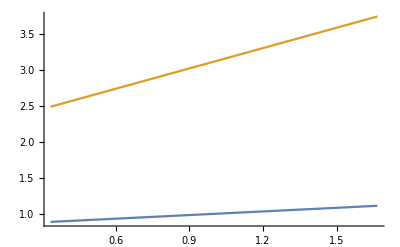

```mathematica
Plot[thePoly,Evaluate[{kk,kLow,kHigh}/.jetDetSubs]]
```

### Stochastic Model

#### Model Equations

```mathematica
juddStoEqn=Join[juddDetEqn/.AA->
AA*theta[t],{Log[theta[t]]-(rho* Log[theta[t-1]]+eta*eps[prod][t])}];
newWeightedStochasticBasis[juddStoMod,juddStoEqn];
```

```mathematica
{{stateVar,nonStateVar,theShock},modEqns}=GenerateModelCode[juddStoMod];
```

"c:\Program Files\Java\jdk1.7.0_51\bin\javac"  @S:/tryBenchWindows/projectionJLinkWin/javaSource/theArgs  -target 1.7 ./juddStoMod.java

```mathematica
modStoParams={AA,alpha,beta,gamma,rho,eta}//.(jetStoSubs=Join[jetDetSubs,{rho->.95,thetaLow->E^(epsLow/(1-rho)),thetaHigh->E^(epsHigh/(1-rho)),epsHigh->3*stdDev,epsLow->-3*stdDev,stdDev->0.000000004,eta->1,theMean->{0},integOrders->{10}}]);
modEqns[updateParams[modStoParams]]
```

#### Projection Method Specification

```mathematica
polyRange={{kLow,kHigh},
{thetaLow,thetaHigh}}//.jetStoSubs;
initPower={0,0};
shockPower={0};
juddBasisSto00=GenerateBasis[stateVar,polyRange//.jetStoSubs,initPower,theShock,theMean//.jetStoSubs,{stdDev}//.jetStoSubs,integOrders//.jetStoSubs,shockPower,nonStateVar]
simp=JavaNew["gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy"];
```

«JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.WeightedStochasticBasis]»

#### Polynomial Weights Computation

```mathematica
resTry[kkGuess_,thetaGuess_,ccGuess_]:=With[{resTry=ComputeInitialCollocationWeights[juddBasisSto00,{{kkGuess},{thetaGuess},{ccGuess}},modEqns,simp]},{resTry[isConvergedQ[]],resTry}]
```

```mathematica
{ig,theStoRes}=resTry[1,1,3.2]
wts00=theStoRes[getResWeights[]];
```

{True,«JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.ProjectionResults]»}

```mathematica
nxtPow={0,1};initWts05=nxtWts[wts00,initPower,nxtPow];
```

```mathematica
shockPower={0};
juddBasisSto=GenerateBasis[stateVar,polyRange//.jetStoSubs,nxtPow,theShock,theMean//.jetStoSubs,{stdDev}//.jetStoSubs,integOrders//.jetStoSubs,shockPower,nonStateVar];
```

```mathematica
resTry05=ComputeInitialCollocationWeights[juddBasisSto,initWts05,modEqns,simp];
resTry05[isConvergedQ[]]
```

True

```mathematica
Dimensions @ Transpose[sillly[[2]],{3,2,1}]
```

{1,6,2}

```mathematica
TableForm[Transpose[sillly[[2]],{3,2,1}][[1,All,Range[2]]]]
```

0. | -8.88178×10^-16
0. | 0.
-8.88178×10^-16 | -7.22722×10^-7
-8.88178×10^-16 | 7.22722×10^-7
-1.69706×10^-7 | -1.42109×10^-14
1.69706×10^-7 | -1.43219×10^-14

```mathematica
sillly=getAllDFVals[resTry05]
```

{{{{1.,-4.21053,1.},{2.2644,-3.0192,1.11022×10^-16},{0.,1.,0.}}},{{{1.,0.707107,-4.21053,-2.97729,1.,0.707107},{1.,-0.707107,-4.21053,2.97729,1.,-0.707107},{2.27148,1.60618,-3.02864,-2.14157,-3.33067×10^-16,0.633694},{2.27148,-1.60618,-3.02864,2.14157,-3.33067×10^-16,-0.633694},{0.,0.,1.,0.707107,0.,0.},{0.,0.,1.,-0.707107,0.,0.}},{{1.,0.707107,-4.21053,-2.97729,1.,0.707107},{1.,-0.707107,-4.21053,2.97729,1.,-0.707107},{2.27148,1.60618,-7.28732,-5.15291,-2.13855×10^-7,-9.71965×10^-8},{2.27148,-1.60618,-7.28732,5.15291,2.13855×10^-7,-9.7867×10^-8},{0.,0.,1.,0.707107,0.,0.},{0.,0.,1.,-0.707107,0.,0.}}}}

```mathematica
Dimensions @ Transpose[sillly[[2]],{3,2,1}]
```

{6,6,2}

```mathematica
TableForm[Transpose[sillly[[2]],{3,2,1}][[All,All,Range[2]]]]
```

1.
1. | 1.
1. | 2.27148
2.27148 | 2.27148
2.27148 | 0.
0. | 0.
0.
0.707107
0.707107 | -0.707107
-0.707107 | 1.60618
1.60618 | -1.60618
-1.60618 | 0.
0. | 0.
0.
-4.21053
-4.21053 | -4.21053
-4.21053 | -3.02864
-7.28732 | -3.02864
-7.28732 | 1.
1. | 1.
1.
-2.97729
-2.97729 | 2.97729
2.97729 | -2.14157
-5.15291 | 2.14157
5.15291 | 0.707107
0.707107 | -0.707107
-0.707107
1.
1. | 1.
1. | -3.33067×10^-16
-2.13855×10^-7 | -3.33067×10^-16
2.13855×10^-7 | 0.
0. | 0.
0.
0.707107
0.707107 | -0.707107
-0.707107 | 0.633694
-9.71965×10^-8 | -0.633694
-9.7867×10^-8 | 0.
0. | 0.
0.

```mathematica
computeChebCoeffs[Cos[#1]&,{2},{{-1,1}}]
```

{1/3 (1+2 Cos[(√3)/2]),0,2/3 (-1+Cos[(√3)/2])}

```mathematica
<<ProjectionInterface`
```

temp export of kronProd

getAllDFVals::shdw: Symbol "getAllDFVals" appears in multiple contexts {"ProjectionInterface`", "Global`"}; definitions in context "ProjectionInterface`" may shadow or be shadowed by other definitions.

why not numbers?

why eval of shock t+1?

done reading ProjectionInterface

```mathematica
Options[ListPlot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DataRange→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,InterpolationOrder→None,Joined→False,LabelStyle→{},MaxPlotPoints→∞,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→None,PlotMarkers→None,PlotRange→Automatic,PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{}}

```mathematica
<<ProjectionInterface`
```

temp export of kronProd

why not numbers?

why eval of shock t+1?

done reading ProjectionInterface

```mathematica
thePoly=genPolys[juddBasisSto[getTheState[]],resTry05[getResWeights[]]]
```

{-0.333333+1.33333 theta,5.29058×10^-10+1. theta,0.333333+2.87719 theta}

```mathematica
thePoly//Dimensions
```

{3}

```mathematica
Plot3D[thePoly,Evaluate[{theta,thetaLow,thetaHigh}//.jetStoSubs],Evaluate[{kk,kLow,kHigh}//.jetStoSubs]]
```

-Graphics3D-

### Simplest Model

#### Model Equations

```mathematica
simpleStoEqn={xxx[t]-(.5xxx[t-1]+0.1xxx[t+1]+eps[simpVar][t])};
newWeightedStochasticBasis[simpleStoMod,simpleStoEqn];
```

```mathematica
{{stateVar,nonStateVar,theShock},modEqns}=GenerateModelCode[simpleStoMod];
```

"c:\Program Files\Java\jdk1.7.0_51\bin\javac"  @S:/tryBenchWindows/projectionJLinkWin/javaSource/theArgs  -target 1.7 ./simpleStoMod.java

"c:\Program Files\Java\jdk1.7.0_51\bin\javac"  @S:/tryBenchWindows/projectionJLinkWin/javaSource/theArgs  -target 1.7 ./simpleStoMod.java

"c:\Program Files\Java\jdk1.7.0_51\bin\javac"  @S:/tryBenchWindows/projectionJLinkWin/javaSource/theArgs  -target 1.7 ./simpleStoMod.java

```mathematica
debugEqCode["simpleStoMod",{-0.5 xxx[-1+t]-0.1xxx[t+1]+xxx[t]-eps[simpVar][t]},{{xxx},{simpVar$Shock}}];
```

```mathematica
modStoParams={}//.(simpStoSubs={xLow->0,xHigh->1,rho->.95,stdDev->0.000000004,theMean->{0},integOrders->{10}});
modEqns[updateParams[modStoParams]]
```

#### Projection Method Specification

```mathematica
polyRange={{xLow,xHigh}}//.simpStoSubs;
initPower={2};
shockPower={0};
simpleBasisSto00=GenerateBasis[stateVar,polyRange//.simpStoSubs,initPower,theShock,theMean//.simpStoSubs,{stdDev}//.simpStoSubs,integOrders//.simpStoSubs,shockPower,nonStateVar]
simp=JavaNew["gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy"];
```

«JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.WeightedStochasticBasis]»

```mathematica
<<ProjectionInterface`
```

temp export of kronProd

why not numbers?

why eval of shock t+1?

done reading ProjectionInterface

#### basis calcs

```mathematica
gtPolyRanges[simpleBasisSto00]
```

{{0.,1.},{-1.94379×10^-8,1.94379×10^-8}}

```mathematica
With[{it=gtXFormedChebSubs[simpleBasisSto00]},{it,Methods[it]}]//Simplify
```

{{{xxx→0.933013,simpVar$Shock→0.},{xxx→0.5,simpVar$Shock→0.},{xxx→0.0669873,simpVar$Shock→0.}},Methods[{{xxx→0.933013,simpVar$Shock→0.},{xxx→0.5,simpVar$Shock→0.},{xxx→0.0669873,simpVar$Shock→0.}}]}

```mathematica
With[{it=gtPolyOrdersForOuterProduct[simpleBasisSto00]},{it,Methods[it]}]//Simplify
```

{{{0,0},{1,0},{2,0}},Methods[{{0,0},{1,0},{2,0}}]}

```mathematica
With[{it=gtPolys[simpleBasisSto00]},{it,Methods[it]}]//Simplify
```

{{1.,-1.+2. xxx,1.-8. xxx+8. xxx^2},Methods[{1.,-1.+2. xxx,1.-8. xxx+8. xxx^2}]}

```mathematica
With[{it=gtXFormedChebSubs[simpleBasisSto00]},{it,Methods[it]}]//Simplify
```

{{{xxx→0.933013,simpVar$Shock→0.},{xxx→0.5,simpVar$Shock→0.},{xxx→0.0669873,simpVar$Shock→0.}},Methods[{{xxx→0.933013,simpVar$Shock→0.},{xxx→0.5,simpVar$Shock→0.},{xxx→0.0669873,simpVar$Shock→0.}}]}

```mathematica
With[{it=gtXFormedChebNodes[simpleBasisSto00]},{it,Methods[it]}]//Simplify
```

{{{0.933013,0.},{0.5,0.},{0.0669873,0.}},Methods[{{0.933013,0.},{0.5,0.},{0.0669873,0.}}]}

```mathematica
With[{it=gtPolysAtPts[simpleBasisSto00]},{it,Methods[it]}]//Simplify
```

{{{1.,1.,1.},{0.866025,6.12323×10^-17,-0.866025},{0.5,-1.,0.5}},Methods[{{1.,1.,1.},{0.866025,6.12323×10^-17,-0.866025},{0.5,-1.,0.5}}]}

```mathematica
With[{it=mmaPolysAtPts[simpleBasisSto00]},{it,Methods[it]}]//Simplify
```

{{{1.,1.,1.},{0.866025,0.,-0.866025},{0.5,-1.,0.5}},Methods[{{1.,1.,1.},{0.866025,0.,-0.866025},{0.5,-1.,0.5}}]}

#### choose wts

```mathematica
tryMat={{1,1,0}};
```

#### time t

```mathematica
With[{it=mmaStateVarsTimeTAtNodes[simpleBasisSto00,tryMat]},{it,Methods[it]}]//Simplify
```

{{{1.86603,0},{1.,0},{0.133975,0}},Methods[{{1.86603,0},{1.,0},{0.133975,0}}]}

```mathematica
With[{it=gtStateVarsTimeTAtNodes[simpleBasisSto00,tryMat]},{it,Methods[it]}]//Simplify
```

{{{1.86603,0.},{1.,0.},{0.133975,0.}},Methods[{{1.86603,0.},{1.,0.},{0.133975,0.}}]}

```mathematica
With[{it=mmaPolysAtOtherPts[simpleBasisSto00,gtXFormedChebNodes[simpleBasisSto00]]},{it,Methods[it]}]//Simplify
```

{{{1.,1.,1.},{0.866025,0.,-0.866025},{0.5,-1.,0.5}},Methods[{{1.,1.,1.},{0.866025,0.,-0.866025},{0.5,-1.,0.5}}]}

```mathematica
Transpose[tryMat . mmaPolysAtOtherPts[simpleBasisSto00,gtXFormedChebNodes[simpleBasisSto00]]]
```

{{1.86603},{1.},{0.133975}}

### time t+1

```mathematica
gtStateVarsTimeTP1AtNodes[simpleBasisSto00,tryMat]
```

{{3.73205},{2.},{0.267949}}

```mathematica
mmaStateVarsTimeTP1AtNodes[simpleBasisSto00,tryMat]
```

{{3.73205},{2.},{0.267949}}

```mathematica
tryMat . mmaPolysAtOtherPts[simpleBasisSto00,gtXFormedChebNodes[simpleBasisSto00]]
```

{{1.86603,1.,0.133975}}

```mathematica
With[{it=ArrayFlatten[{{gtStateVarsTimeTP1AtNodes[simpleBasisSto00,tryMat],ConstantArray[0,{3,1}]}}]},{it,Methods[it]}]//Simplify
```

{{{3.73205,0},{2.,0},{0.267949,0}},Methods[{{3.73205,0},{2.,0},{0.267949,0}}]}

```mathematica
With[{it=tryMat.mmaPolysAtOtherPts[simpleBasisSto00,ArrayFlatten[{{gtStateVarsTimeTP1AtNodes[simpleBasisSto00,tryMat],ConstantArray[0,{3,1}]}}]]},{it,Methods[it]}]//Simplify
```

{{{7.4641,4.,0.535898}},Methods[{{7.4641,4.,0.535898}}]}

```mathematica
With[{it=gtNStateVarsTimeTP1AtNodes[simpleBasisSto00,{{1,1,1}}]},{it,Methods[it]}]//Simplify
```

{{{}},Methods[{{}}]}

```mathematica
With[{it=mmaPolysAtOtherPts[simpleBasisSto00,gtXFormedChebNodes[simpleBasisSto00]]},{it,Methods[it]}]//Simplify
```

{{{1.,1.,1.},{0.866025,0.,-0.866025},{0.5,-1.,0.5}},Methods[{{1.,1.,1.},{0.866025,0.,-0.866025},{0.5,-1.,0.5}}]}

```mathematica
tryMat . mmaPolysAtOtherPts[simpleBasisSto00,gtXFormedChebNodes[simpleBasisSto00]]
```

{{1.86603,1.,0.133975}}

```mathematica
With[{it=gtStateVarPolys[simpleBasisSto00]},{it,Methods[it]}]//Simplify;
```

```mathematica
Methods[simpleBasisSto00]
```

static int[][] allPowers(int[])
static int[] dropEnd(int[])
boolean equals(Object)
static int[] expand(int[], int, int)
Class getClass()
Jama.Matrix getDrvPolyNowDrvMatrix(int, int, int)
Jama.Matrix getDrvPolyNowValMatrix(int, int, int)
double[] getGaussHermiteMean()
double[] getGaussHermiteStDev()
int getMaxShrink()
java.util.List getNewtonIters()
gov.frb.ma.msu.ProjectionMethodToolsJava.StrategyIterSequenceInfo getNewtonItersSeq()
int getNewtonSteps()
int getNumberOfShocks()
double[][] getRanges()
int[] getShockVarLocs()
double getShrinkFactor()
gov.frb.ma.msu.ProjectionMethodToolsJava.GaussHermite getTheGaussHermite()
gov.frb.ma.msu.ProjectionMethodToolsJava.NonStateVariablePolynomials getTheNonState()
double[] getTheShockVals()
gov.frb.ma.msu.ProjectionMethodToolsJava.StateVariablePolynomials getTheState()
int getVarIndex(gov.frb.ma.msu.ProjectionMethodToolsJava.VarTime) throws gov.frb.ma.msu.ProjectionMethodToolsJava.ProjectionRuntimeException
int hashCode()
gov.frb.ma.msu.ProjectionMethodToolsJava.Basis incPowers(gov.frb.ma.msu.ProjectionMethodToolsJava.StateVariablePolynomials, int[]) throws gov.frb.ma.msu.ProjectionMethodToolsJava.ProjectionRuntimeException
gov.frb.ma.msu.ProjectionMethodToolsJava.WeightedStochasticBasis incPowers(int[]) throws gov.frb.ma.msu.ProjectionMethodToolsJava.ProjectionRuntimeException
static int indexPower(int[], int, int[])
boolean isInNeedOfShockUpdatesQ()
boolean isPerfectForesightQ()
void multiArrayCopy(double[][], double[][])
void notify()
void notifyAll()
int numNodesNow()
int numVarsNow()
static int[] rawPows(int)
void setAllWeights(double[][])
void setAllWeights(int)
void setGaussHermiteMean(double[])
void setGaussHermiteStDev(double[])
void setInNeedOfShockUpdatesQ(boolean)
void setMaxShrink(int)
void setNewtonIters(java.util.List)
void setNewtonItersSeq(gov.frb.ma.msu.ProjectionMethodToolsJava.StrategyIterSequenceInfo)
void setNewtonSteps(int)
void setNumberOfShocks(int)
void setPerfectForesightQ(boolean)
void setShockVarLocs()
void setShockVarLocs(int[])
void setShrinkFactor(double)
void setTheGaussHermite(gov.frb.ma.msu.ProjectionMethodToolsJava.GaussHermite)
void setTheNonState(gov.frb.ma.msu.ProjectionMethodToolsJava.NonStateVariablePolynomials)
void setTheNonStateWeights(double[][]) throws gov.frb.ma.msu.ProjectionMethodToolsJava.ProjectionRuntimeException
void setTheShockVals(double[])
void setTheState(gov.frb.ma.msu.ProjectionMethodToolsJava.StateVariablePolynomials)
void setTheStateWeights(double[][]) throws gov.frb.ma.msu.ProjectionMethodToolsJava.ProjectionRuntimeException
double[][][] solveParamsRange(double[][], gov.frb.ma.msu.ProjectionMethodToolsJava.DoEqns, double[], double[], int) throws gov.frb.ma.msu.ProjectionMethodToolsJava.ProjectionRuntimeException
String toString()
void updateForShocks(gov.frb.ma.msu.ProjectionMethodToolsJava.DoEqns, int[], double[]) throws gov.frb.ma.msu.ProjectionMethodToolsJava.ProjectionRuntimeException
double[] updateParams(double[], double[], int, int)
void wait(long, int) throws InterruptedException
void wait(long) throws InterruptedException
void wait() throws InterruptedException

```mathematica
Methods[simpleBasisSto00]
```

static int[][] allPowers(int[])
static int[] dropEnd(int[])
boolean equals(Object)
static int[] expand(int[], int, int)
Class getClass()
Jama.Matrix getDrvPolyNowDrvMatrix(int, int, int)
Jama.Matrix getDrvPolyNowValMatrix(int, int, int)
double[] getGaussHermiteMean()
double[] getGaussHermiteStDev()
int getMaxShrink()
java.util.List getNewtonIters()
gov.frb.ma.msu.ProjectionMethodToolsJava.StrategyIterSequenceInfo getNewtonItersSeq()
int getNewtonSteps()
int getNumberOfShocks()
double[][] getRanges()
int[] getShockVarLocs()
double getShrinkFactor()
gov.frb.ma.msu.ProjectionMethodToolsJava.GaussHermite getTheGaussHermite()
gov.frb.ma.msu.ProjectionMethodToolsJava.NonStateVariablePolynomials getTheNonState()
double[] getTheShockVals()
gov.frb.ma.msu.ProjectionMethodToolsJava.StateVariablePolynomials getTheState()
int getVarIndex(gov.frb.ma.msu.ProjectionMethodToolsJava.VarTime) throws gov.frb.ma.msu.ProjectionMethodToolsJava.ProjectionRuntimeException
int hashCode()
gov.frb.ma.msu.ProjectionMethodToolsJava.Basis incPowers(gov.frb.ma.msu.ProjectionMethodToolsJava.StateVariablePolynomials, int[]) throws gov.frb.ma.msu.ProjectionMethodToolsJava.ProjectionRuntimeException
gov.frb.ma.msu.ProjectionMethodToolsJava.WeightedStochasticBasis incPowers(int[]) throws gov.frb.ma.msu.ProjectionMethodToolsJava.ProjectionRuntimeException
static int indexPower(int[], int, int[])
boolean isInNeedOfShockUpdatesQ()
boolean isPerfectForesightQ()
void multiArrayCopy(double[][], double[][])
void notify()
void notifyAll()
int numNodesNow()
int numVarsNow()
static int[] rawPows(int)
void setAllWeights(double[][])
void setAllWeights(int)
void setGaussHermiteMean(double[])
void setGaussHermiteStDev(double[])
void setInNeedOfShockUpdatesQ(boolean)
void setMaxShrink(int)
void setNewtonIters(java.util.List)
void setNewtonItersSeq(gov.frb.ma.msu.ProjectionMethodToolsJava.StrategyIterSequenceInfo)
void setNewtonSteps(int)
void setNumberOfShocks(int)
void setPerfectForesightQ(boolean)
void setShockVarLocs()
void setShockVarLocs(int[])
void setShrinkFactor(double)
void setTheGaussHermite(gov.frb.ma.msu.ProjectionMethodToolsJava.GaussHermite)
void setTheNonState(gov.frb.ma.msu.ProjectionMethodToolsJava.NonStateVariablePolynomials)
void setTheNonStateWeights(double[][]) throws gov.frb.ma.msu.ProjectionMethodToolsJava.ProjectionRuntimeException
void setTheShockVals(double[])
void setTheState(gov.frb.ma.msu.ProjectionMethodToolsJava.StateVariablePolynomials)
void setTheStateWeights(double[][]) throws gov.frb.ma.msu.ProjectionMethodToolsJava.ProjectionRuntimeException
double[][][] solveParamsRange(double[][], gov.frb.ma.msu.ProjectionMethodToolsJava.DoEqns, double[], double[], int) throws gov.frb.ma.msu.ProjectionMethodToolsJava.ProjectionRuntimeException
String toString()
void updateForShocks(gov.frb.ma.msu.ProjectionMethodToolsJava.DoEqns, int[], double[]) throws gov.frb.ma.msu.ProjectionMethodToolsJava.ProjectionRuntimeException
double[] updateParams(double[], double[], int, int)
void wait(long, int) throws InterruptedException
void wait(long) throws InterruptedException
void wait() throws InterruptedException

```mathematica
Methods[modEqns]
```

boolean equals(Object)
Class getClass()
double[] getParams()
int hashCode()
void noNans(gov.frb.ma.msu.ProjectionMethodToolsJava.WeightedStochasticBasis, double[][], double[][]) throws gov.frb.ma.msu.ProjectionMethodToolsJava.ProjectionRuntimeException
void notify()
void notifyAll()
String toString()
void updateParams(double[])
gov.frb.ma.msu.ProjectionMethodToolsJava.EquationValDrv updateValDrv(gov.frb.ma.msu.ProjectionMethodToolsJava.StochasticBasis) throws gov.frb.ma.msu.ProjectionMethodToolsJava.ProjectionRuntimeException
void wait(long, int) throws InterruptedException
void wait(long) throws InterruptedException
void wait() throws InterruptedException

```mathematica
Class[modEqns]
```

Class[«JavaObject[simpleStoMod]»]

## ignow

#### Polynomial Weights Computation

```mathematica
resTry[xGuess_]:=With[{resTry=ComputeInitialCollocationWeights[simpleBasisSto00,{{xGuess}},modEqns,simp]},{resTry[isConvergedQ[]],resTry}]
```

```mathematica
{ig,theStoRes}=resTry[.5]
wts00=theStoRes[getResWeights[]];
```

{True,«JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.ProjectionResults]»}

```mathematica
sillly=getAllXVals[theStoRes]
```

{{{{0.}}}}

```mathematica
nxtPow={0,1};initWts05=nxtWts[wts00,initPower,nxtPow];
```

```mathematica
shockPower={0};
simpleBasisSto=GenerateBasis[stateVar,polyRange//.simpStoSubs,nxtPow,theShock,theMean//.simpStoSubs,{stdDev}//.simpStoSubs,integOrders//.simpStoSubs,shockPower,nonStateVar];
```

Java::excptn: A Java exception occurred: "gov.frb.ma.msu.ProjectionMethodToolsJava.ProjectionRuntimeException: xx length=2 different length than thePolyOrders length=3\n\tat gov.frb.ma.msu.ProjectionMethodToolsJava.ChebyshevPolynomial.chkLength(ChebyshevPolynomial.java:147)\n\tat gov.frb.ma.msu.ProjectionMethodToolsJava.ChebyshevPolynomial.evaluateBasisAtEvalPoints(ChebyshevPolynomial.java:135)\n\tat gov.frb.ma.msu.ProjectionMethodToolsJava.ChebyshevPolynomial.evaluateBasisAtEvalPoints(ChebyshevPolynomial.java:122)\n\tat gov.frb.ma.msu.ProjectionMethodToolsJava.ChebyshevPolysAtEvalPoints.<init>(ChebyshevPolysAtEvalPoints.java:25)\n\tat gov.frb.ma.msu.ProjectionMethodToolsJava.GridPointsSpec.<init>(GridPointsSpec.java:23)\n\tat gov.frb.ma.msu.ProjectionMethodToolsJava.WeightedStochasticBasis.<init>(WeightedStochasticBasis.java:137)\n\tat gov.frb.ma.msu.ProjectionMethodToolsJava.WeightedStochasticBasis.<init>(WeightedStochasticBasis.java:167)\n\tat sun.reflect.NativeConstructorAccessorImpl.newInstance0(Native Method)\n\tat sun.reflect.NativeConstructorAccessorImpl.newInstance(Unknown Source)\n\tat sun.reflect.DelegatingConstructorAccessorImpl.newInstance(Unknown Source)\n\tat java.lang.reflect.Constructor.newInstance(Unknown Source)".

JavaNew::fail: Error calling constructor for class "gov.frb.ma.msu.ProjectionMethodToolsJava.WeightedStochasticBasis".

```mathematica
resTry05=ComputeInitialCollocationWeights[simpleBasisSto,initWts05,modEqns,simp];
resTry05[isConvergedQ[]]
```

ComputeInitialCollocationWeights[$Failed,nxtWts[Null,{0},{0,1}],«JavaObject[simpleStoMod]»,«JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy]»][isConvergedQ[]]

```mathematica
Dimensions @ Transpose[sillly[[2]],{3,2,1}]
```

Part::partd: Part specification sillly ⟦ 2 ⟧ is longer than depth of object.

{2}

```mathematica
TableForm[Transpose[sillly[[2]],{3,2,1}][[1,All,Range[2]]]]
```

Part::partd: Part specification sillly ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification Transpose[sillly ⟦ 2 ⟧, {3, 2, 1}] ⟦ 1, All, {1, 2} ⟧ is longer than depth of object.

Transpose[sillly⟦2⟧,{3,2,1}]⟦1,All,{1,2}⟧

```mathematica
sillly=getAllDFVals[resTry05]
```

getAllDFVals[ComputeInitialCollocationWeights[$Failed,nxtWts[Null,{0},{0,1}],«JavaObject[simpleStoMod]»,«JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy]»]]

```mathematica
Dimensions @ Transpose[sillly[[2]],{3,2,1}]
```

Part::partw: Part 2 of ComputeInitialCollocationWeights[$Failed, nxtWts[Null, {0}, {0, 1}], InterpretationBox[« JavaObject[simpleStoMod] », JLink`Objects`vm1`JavaObject28411838798495745], InterpretationBox[« JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy] », JLink`Objects`vm1`JavaObject23264873873932289]] does not exist.

{2}

```mathematica
TableForm[Transpose[sillly[[2]],{3,2,1}][[All,All,Range[2]]]]
```

Part::partw: Part 2 of ComputeInitialCollocationWeights[$Failed, nxtWts[Null, {0}, {0, 1}], InterpretationBox[« JavaObject[simpleStoMod] », JLink`Objects`vm1`JavaObject28411838798495745], InterpretationBox[« JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy] », JLink`Objects`vm1`JavaObject23264873873932289]] does not exist.

Part::partw: Part {1, 2} of ComputeInitialCollocationWeights[$Failed, nxtWts[Null, {0}, {0, 1}], InterpretationBox[« JavaObject[simpleStoMod] », JLink`Objects`vm1`JavaObject28411838798495745], InterpretationBox[« JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy] », JLink`Objects`vm1`JavaObject23264873873932289]] does not exist.

Transpose[getAllDFVals[ComputeInitialCollocationWeights[$Failed,nxtWts[Null,{0},{0,1}],«JavaObject[simpleStoMod]»,«JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy]»]]⟦2⟧,{3,2,1}]⟦All,All,{1,2}⟧

```mathematica
computeChebCoeffs[Cos[#1]&,{2},{{-1,1}}]
```

{1/3 (1+2 Cos[(√3)/2]),0,2/3 (-1+Cos[(√3)/2])}

```mathematica
<<ProjectionInterface`
```

temp export of kronProd

why not numbers?

why eval of shock t+1?

done reading ProjectionInterface

```mathematica
Options[ListPlot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DataRange→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,InterpolationOrder→None,Joined→False,LabelStyle→{},MaxPlotPoints→∞,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→None,PlotMarkers→None,PlotRange→Automatic,PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{}}

```mathematica
<<ProjectionInterface`
```

temp export of kronProd

why not numbers?

why eval of shock t+1?

done reading ProjectionInterface

```mathematica
thePoly=genPolys[simpleBasisSto[getTheState[]],resTry05[getResWeights[]]]
```

genPolys[$Failed[getTheState[]],ComputeInitialCollocationWeights[$Failed,nxtWts[Null,{0},{0,1}],«JavaObject[simpleStoMod]»,«JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy]»][getResWeights[]]]

```mathematica
thePoly//Dimensions
```

{2}

```mathematica
Plot3D[thePoly,Evaluate[{theta,thetaLow,thetaHigh}//.simpStoSubs],Evaluate[{kk,kLow,kHigh}//.simpStoSubs]]
```

Plot3D::plln: Limiting value thetaLow in {theta, thetaLow, thetaHigh} is not a machine-sized real number.

Plot3D[thePoly,{theta,thetaLow,thetaHigh},{kk,kLow,kHigh}]

## ignore for now

```mathematica
{flg,res}=indFunc00[.2,1.,simp];
nis=res[getTheStrategyIters[]];
them=nis[get[#]]&/@Range[0,nis[size[]]-1];
ani=them[[1]];
displayStrategyIterInfo[getStrategyInfo[ani,#]]&/@Range[getNumNewtonIters[ani]];
getNumNewtonIters[ani]
```

1

```mathematica
{flg,aRes}=indFunc00[1,3.21053,simp]
```

{-1,«JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.ProjectionResults]»}

```mathematica
aRes[getResWeights[]]
```

```mathematica
si=aRes[getTheStrategyIters[]]
```

«JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.StrategyIterSequenceInfo]»

```mathematica
aRes[isConvergedQ[]]
```

False

```mathematica
ni=si[getNewtonIters[]]
```

«JavaObject[java.util.ArrayList]»

```mathematica
ni[toArray[]]
```

{}

```mathematica
indFunc00[xx_?NumberQ,yy_?NumberQ]:=
With[{restry=ComputeInitialCollocationWeights[juddBasisSto00,{{xx},{yy}},modEqns,JavaNew["gov.frb.ma.msu.ProjectionTools.SimpleFindZeroStrategy"]]},{If[MatrixQ[restry[getResWeights[]]]==True,1,-1],restry}]
```

```mathematica
indFunc00[xx_?NumberQ,yy_?NumberQ,strat_?JavaObjectQ]:=With[{restry=ComputeInitialCollocationWeights[juddBasisSto00,{{xx},{yy}},modEqns,strat]},{If[MatrixQ[restry[getResWeights[]]]==True,1,-1],restry}]

retrieveIters[stratInfo_?JavaObjectQ]:=With[{nisInfo=stratInfo[getStrategyIters[]]},nisInfo[get[0]]]

retrieveIters[stratInfo_?JavaObjectQ]:=With[{nisInfo=stratInfo[getStrategyIters[]]},nisInfo[get[0]]]

(*from getmathtowork*)

getStrategyIters[res_?JavaObjectQ]:=res[getTheStrategyIters[]]/;StringMatchQ[ClassName[res],"gov.frb.ma.msu.ProjectionMethodToolsJava.someResults"]
getStrategySeq[stratIts_?JavaObjectQ,num_Integer]:=stratIts[get[num-1]]/;StringMatchQ[ClassName[stratIts],"gov.frb.ma.msu.ProjectionMethodToolsJava.StrategyIterSequenceInfo"]
getStrategyInfo[nis_?JavaObjectQ,num_Integer]:=nis[get[num-1]]/;StringMatchQ[ClassName[nis],"gov.frb.ma.msu.ProjectionMethodToolsJava.StrategyIterSequenceInfo"]
getNumStrategyIters[nis_?JavaObjectQ]:=nis[size[]]/;StringMatchQ[ClassName[nis],"gov.frb.ma.msu.ProjectionMethodToolsJava.StrategyIterSequenceInfo"]
displayStrategyIterInfo[nis_?JavaObjectQ]:={del=nis[getDelta[]],fVal=nis[getfVal[]],xx=nis[getXx[]],conv=nis[isConvergedQ[]]}/;StringMatchQ[ClassName[nis],"gov.frb.ma.msu.ProjectionMethodToolsJava.StrategyIterInfo"]

getNewtonSeq[stratIts_?JavaObjectQ,num_Integer]:=stratIts[get[num-1]]/;StringMatchQ[ClassName[stratIts],"gov.frb.ma.msu.ProjectionMethodToolsJava.StrategyIterSequenceInfo"]
getNewtonInfo[nis_?JavaObjectQ,num_Integer]:=nis[get[num-1]]/;StringMatchQ[ClassName[nis],"gov.frb.ma.msu.ProjectionMethodToolsJava.NewtonIterSequenceInfo"]
getNumNewtonIters[nis_?JavaObjectQ]:=nis[size[]]/;StringMatchQ[ClassName[nis],"gov.frb.ma.msu.ProjectionMethodToolsJava.NewtonIterSequenceInfo"]
displayNewtonIterInfo[nis_?JavaObjectQ]:={del=nis[getDelta[]],fVal=nis[getfVal[]],xx=nis[getXx[]],conv=nis[isConvergedQ[]]}/;StringMatchQ[ClassName[nis],"gov.frb.ma.msu.ProjectionMethodToolsJava.NewtonIterInfo"]


juddSSSys=juddEqn/.{cc[_]->css,kk[_]->kss,eps[_][_]->0}
FindRoot[juddSSSys//.jetSubs,{kss,1},{css,1}]


simp=JavaNew["gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy"];
{flg,res}=indFunc00[.2,1.,simp];

nis=res[getTheStrategyIters[]];
them=nis[get[#]]&/@Range[0,nis[size[]]-1];
ani=them[[1]];
displayStrategyIterInfo[getStrategyInfo[ani,#]]&/@Range[getNumNewtonIters[ani]];
getNumNewtonIters[ani]
```

juddEqn

ReplaceRepeated::reps: {jetSubs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {juddEqn//. jetSubs} is not a list of numbers with dimensions {1} at {kss, css} = {1., 1.}.

FindRoot[juddSSSys//.jetSubs,{kss,1},{css,1}]

Range::range: Range specification in 0, -1 + ComputeInitialCollocationWeights[juddBasisSto00, {{0.2`}, {1.`}}, modEqns, InterpretationBox[« JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy] », JLink`Objects`vm1`JavaObject29902274876669953]][getTheStrategyIters[]][size[]] does not have appropriate bounds.

Range::range: Range specification in ComputeInitialCollocationWeights[juddBasisSto00, {{0.2`}, {1.`}}, modEqns, InterpretationBox[« JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy] », JLink`Objects`vm1`JavaObject29902274876669953]][getTheStrategyIters[]][get[0]], ComputeInitialCollocationWeights[juddBasisSto00, {{0.2`}, {1.`}}, modEqns, InterpretationBox[« JavaObject[« 63 »] », JLink`Objects`vm1`JavaObject29902274876669953]][getTheStrategyIters[]][« 1 »] does not have appropriate bounds.

Range::range: Range specification in getNumNewtonIters[ComputeInitialCollocationWeights[juddBasisSto00, {{0.2`}, {1.`}}, modEqns, InterpretationBox[« JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy] », JLink`Objects`vm1`JavaObject29902274876669953]][getTheStrategyIters[]][get[0]]] does not have appropriate bounds.

Range::range: Range specification in displayStrategyIterInfo[getStrategyInfo[ComputeInitialCollocationWeights[juddBasisSto00, {{0.2`}, {1.`}}, modEqns, InterpretationBox[« JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy] », JLink`Objects`vm1`JavaObject29902274876669953]][getTheStrategyIters[]][get[0]], getNumNewtonIters[ComputeInitialCollocationWeights[« 1 »][« 19 »[]][get[0]]]]] does not have appropriate bounds.

getNumNewtonIters[ComputeInitialCollocationWeights[juddBasisSto00,{{0.2},{1.}},modEqns,«JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.SimpleFindZeroStrategy]»][getTheStrategyIters[]][get[0]]]

```mathematica
noShockjuddBasis00=GenerateBasis[{stateVar,nonStateVar},polyRange,initPower]

juddBasis00=GenerateBasis[stateVar,polyRange,initPower,theShocks,{0},{0.000001},{10},{0},nonStateVar]
```

«JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.WeightedStochasticBasis]»

GenerateBasis[{kk,theta},{{0.333,1.667},{1.,1.}},{0,0},theShocks,{0},{1.×10^-6},{10},{0},{cc}]

```mathematica
indFunc00[xx_?NumberQ,yy_?NumberQ]:=
With[{restry=ComputeInitialCollocationWeights[juddBasis00,{{xx},{yy}},modEqns,JavaNew["gov.frb.ma.msu.ProjectionTools.SimpleFindZeroStrategy"]]},{If[MatrixQ[restry[getResWeights[]]]==True,1,-1],restry}]
```

```mathematica
retrieveIters[stratInfo_?JavaObjectQ]:=With[{nisInfo=stratInfo[getStrategyIters[]]},nisInfo[get[0]]]

retrieveIters[stratInfo_?JavaObjectQ]:=With[{nisInfo=stratInfo[getStrategyIters[]]},nisInfo[get[0]]]

(*from getmathtowork*)

getStrategyIters[res_?JavaObjectQ]:=res[getTheStrategyIters[]]/;StringMatchQ[ClassName[res],"gov.frb.ma.msu.ProjectionMethodToolsJava.someResults"]
getStrategySeq[stratIts_?JavaObjectQ,num_Integer]:=stratIts[get[num-1]]/;StringMatchQ[ClassName[stratIts],"gov.frb.ma.msu.ProjectionMethodToolsJava.StrategyIterSequenceInfo"]
getStrategyInfo[nis_?JavaObjectQ,num_Integer]:=nis[get[num-1]]/;StringMatchQ[ClassName[nis],"gov.frb.ma.msu.ProjectionMethodToolsJava.StrategyIterSequenceInfo"]
getNumStrategyIters[nis_?JavaObjectQ]:=nis[size[]]/;StringMatchQ[ClassName[nis],"gov.frb.ma.msu.ProjectionMethodToolsJava.StrategyIterSequenceInfo"]
displayStrategyIterInfo[nis_?JavaObjectQ]:={del=nis[getDelta[]],fVal=nis[getfVal[]],xx=nis[getXx[]],conv=nis[isConvergedQ[]]}/;StringMatchQ[ClassName[nis],"gov.frb.ma.msu.ProjectionMethodToolsJava.StrategyIterInfo"]

getNewtonSeq[stratIts_?JavaObjectQ,num_Integer]:=stratIts[get[num-1]]/;StringMatchQ[ClassName[stratIts],"gov.frb.ma.msu.ProjectionMethodToolsJava.StrategyIterSequenceInfo"]
getNewtonInfo[nis_?JavaObjectQ,num_Integer]:=nis[get[num-1]]/;StringMatchQ[ClassName[nis],"gov.frb.ma.msu.ProjectionMethodToolsJava.NewtonIterSequenceInfo"]
getNumNewtonIters[nis_?JavaObjectQ]:=nis[size[]]/;StringMatchQ[ClassName[nis],"gov.frb.ma.msu.ProjectionMethodToolsJava.NewtonIterSequenceInfo"]
displayNewtonIterInfo[nis_?JavaObjectQ]:={del=nis[getDelta[]],fVal=nis[getfVal[]],xx=nis[getXx[]],conv=nis[isConvergedQ[]]}/;StringMatchQ[ClassName[nis],"gov.frb.ma.msu.ProjectionMethodToolsJava.NewtonIterInfo"]
```

```mathematica
noShockjuddBasis00=GenerateBasis[{stateVar,nonStateVar},polyRange,initPower]

juddBasis00=GenerateBasis[stateVar,polyRange,initPower,theShocks,{0},{0.000001},{10},{0},nonStateVar]
```

«JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.WeightedStochasticBasis]»

GenerateBasis[{kk,theta},{{0.333,1.667},{1.,1.}},{0,0},theShocks,{0},{1.×10^-6},{10},{0},{cc}]

```mathematica
{flg,aRes}=indFunc00[1,2.21053,simp]
```

{-1,«JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.ProjectionResults]»}

```mathematica
aRes[getResWeights[]]
```

## Burnside Model

```mathematica
burnsideEqns={-1*y[t]+beta*(E^(theta*(x[t+1]))*(1+y[t+1])),eps[xx][t]*eta+rho (x[-1+t]-xbar)-(x[t]-xbar)};

ericMoms=With[{stdev=0348/10000},Table[mom[xx,ii]->Moment[NormalDistribution[0,stdev],ii],{ii,10}]];

zapMoms=With[{stdev=0348/10000},Table[mom$eps$xx[ii]=Moment[NormalDistribution[0,stdev],ii],{ii,10}]];

burnsideSubs=Join[{beta->95/100,rho->-139/1000,theta->-15/10,xbar->0179/10000,sigVal->0348/10000,eta->1}];
```

```mathematica
newWeightedStochasticBasis[burnsideModProj,(burnsideEqns)//.burnsideSubs];

{{stateVars,nonStateVars,shocks},modEqns}=GenerateModelCode[burnsideModProj];

polyRanges={{xLow=0.01,xHigh=1.},{zLow=-.1,zHigh=.1}};
(*initial power of polynomial*)



initPowers={0};
shockPowers={0};
shockMeans={0};
shockStDevs={0348/10000.};
intOrders={10};


burnsideBasis=GenerateBasis[stateVars,polyRanges,initPowers,shocks,shockMeans,shockStDevs,intOrders,shockPowers,nonStateVars]


guessWts={{0.202639},{0.360247}};
res00=ComputeInitialCollocationWeights[burnsideBasis,guessWts,modEqns];
```

"c:\Program Files\Java\jdk1.7.0_51\bin\javac"  @S:/tryBenchWindows/projectionJLinkWin/javaSource/theArgs  -target 1.7 ./burnsideModProj.java

«JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.WeightedStochasticBasis]»

```mathematica
res00[isConvergedQ[]]
```

True

```mathematica
stateVars
```

{x}

```mathematica
nonStateVars
```

{y}

```mathematica
shocks
```

{xx$Shock}

```mathematica
projPoly00=genPolys[res00[getResWeights[]],stateVars,polyRanges,initPowers];
ss00=FindRoot[{x,y}-projPoly00/.xx$Shock->0,{{x,.1},{y,5.}}]
```

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[phiFunc[#3, #1, #2 ⟦ 1 ⟧, #2 ⟦ 2 ⟧] &, {{0}, {{0.01, 1.}, {-0.1, 0.1}}, {"x"}}]; dimensions are 1 and 2.

Outer::heads: Heads List and Function at positions 3 and 2 are expected to be the same.

FindRoot::nlnum: The function value {0.1  - 1.\ {{-0.0498069}, {-43.2059}} . Outer[Times, phiFunc[Slot[« 1 »], Slot[« 1 »], Part[« 2 »], Part[« 2 »]] &, {{0.}, {{« 2 »}, {« 2 »}}, {"x"}}], 5.  - 1.\ {{-0.0498069}, {-43.2059}} . Outer[Times, phiFunc[Slot[« 1 »], Slot[« 1 »], Part[« 2 »], Part[« 2 »]] &, {{0.}, {{« 2 »}, {« 2 »}}, {"x"}}]} is not a list of numbers with dimensions {2} at {x, y} = {0.1, 5.}.

Outer::heads: Heads List and Function at positions 3 and 2 are expected to be the same.

General::stop: Further output of Outer :: heads will be suppressed during this calculation.

FindRoot::nlnum: The function value {0.1  - 1.\ {{-0.0498069}, {-43.2059}} . Outer[Times, phiFunc[Slot[« 1 »], Slot[« 1 »], Part[« 2 »], Part[« 2 »]] &, {{0.}, {{« 2 »}, {« 2 »}}, {"x"}}], 5.  - 1.\ {{-0.0498069}, {-43.2059}} . Outer[Times, phiFunc[Slot[« 1 »], Slot[« 1 »], Part[« 2 »], Part[« 2 »]] &, {{0.}, {{« 2 »}, {« 2 »}}, {"x"}}]} is not a list of numbers with dimensions {2} at {x, y} = {0.1, 5.}.

FindRoot[{x,y}-projPoly00/.xx$Shock→0,{{x,0.1},{y,5.}}]

```mathematica
shocks
```

{xx$Shock}

```mathematica
res00[isConvergedQ[]]
```

True

```mathematica
res00[getResWeights[]]
```

{{-0.0498069},{-43.2059}}

```mathematica
genPolys[res00]
```

genPolys[«JavaObject[gov.frb.ma.msu.ProjectionMethodToolsJava.ProjectionResults]»]

```mathematica
projPoly00
```

{{-0.0498069},{-43.2059}}.Outer[Times,phiFunc[#3,#1,#2⟦1⟧,#2⟦2⟧]&,{{0},{{0.01,1.},{-0.1,0.1}},{x}}]

```mathematica
??phiFunc
```

phiFunc[st_|(st_Symbol|st_?NumberQ),nn_Integer,aa_|(aa_|aa_?NumberQ),bb_|(bb_|bb_?NumberQ)]

phiFunc[ProjectionInterface`Private`st_|(ProjectionInterface`Private`st_Symbol|ProjectionInterface`Private`st_?NumberQ),ProjectionInterface`Private`nn_Integer,ProjectionInterface`Private`aa_|(ProjectionInterface`Private`aa_|ProjectionInterface`Private`aa_?NumberQ),ProjectionInterface`Private`bb_|(ProjectionInterface`Private`bb_|ProjectionInterface`Private`bb_?NumberQ)]:=Table[ChebyshevT[ProjectionInterface`Private`ii,toChebyshevInterval[ProjectionInterface`Private`st,ProjectionInterface`Private`aa,ProjectionInterface`Private`bb]],{ProjectionInterface`Private`ii,0,ProjectionInterface`Private`nn}]
 
phiFunc[ProjectionInterface`Private`st_|(ProjectionInterface`Private`st_Symbol|ProjectionInterface`Private`st_?NumberQ),ProjectionInterface`Private`nn_Integer]:=phiFunc[ProjectionInterface`Private`st,ProjectionInterface`Private`nn,-1,1]